Quick Tour

```mathematica
Needs["Fretica`"]
```

We open simulated single-molecule  data of a FRET-labeled species diffusing though a confocal volume of a microscope. Three subpopulations of equal sizes are present : donor-only,  E=0.5 , and E=0.9

```mathematica
FOpenTTTR[$FreticaExamples<>"\\Sim01.ht3"] 
FMCStrace[{acceptor={1,0},donor={0,1}}(*detection channels*), 1.(*ms binning*),0 (*t1 in sec*),5.(*t2 in sec*)]
FPCH[{acceptor,donor}(*detection channels*),1 (*ms binning*),PlotStyle->{Red,Green}]
```

1

-Graphics-

-Graphics-

The data were simulated assuming a total species concentration of 50 pM  diffusing ( D=0.05 mm^2/ms.) through a laser focus described by a spherical-symmetric 3D Gaussian [  exp(-2 r^2/w0^2) ] with w0=0.4 μm. The molecular brightness at the center of the confocal volume is 100 photons/ms.

Typical Fretica settings for a two channel FRET measurement

```mathematica
FEnablePie[False];
FSetFRETRoutes[{"A","D"}](* detector1: acceptor, detector2: donor*)
FSetRCM[({{1, -0.08}, {0, 1.5}})];(*γ=1.5, Subscript[β, D->A]=0.08, Subscript[β, A->D]=0.*)
FSetDirectAcceptorExcitation[0.04];
```

Burst identification and background determination:

```mathematica
bg=FDetermineBackground[](*returns estimated background rates in counts per seconds*)
nbursts=FFindBurstsDeltaT[0.00015 (*dtmax*),20 (*nmin*),10000(*nmax*)]
bg=FDetermineBackground[](*iteration improves the result*)
nbursts=FFindBurstsDeltaT[0.00015 (*dtmax*),20 (*nmin*),10000(*nmax*)]
bg=FDetermineBackground[](*no significant further improvement*)
nbursts=FFindBurstsDeltaT[0.00015 (*dtmax*),40 (*nmin*),10000(*nmax*)]
```

{1716.39,3138.61,0.,0.,0.,0.}

6968

{1578.63,3044.98,0.,0.,0.,0.}

7039

{1577.97,3044.68,0.,0.,0.,0.}

3316

The 'true' background rates of the simulation are 1500 photons/sec (acceptor) and 3000 photons/sec (donor)

Uncorrected and corrected transfer efficiency histogram

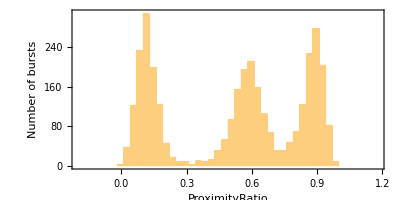

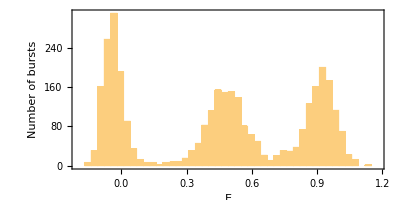

```mathematica
FParamHisto["ProximityRatio",{-0.2,1.2,0.03}]
FParamHisto["E",{-0.2,1.2,0.03}]
```

Fitting of the  corrected transfer efficiency histogram with empirical peak functions:  `Gaussian` and `Lognormal`:

```mathematica
fit=FFitFretHistogram[{-0.2 (*Emin*),1.2 (*Emax*),0.02 (*binning*)},{"G","G","L"},{0,0.5,0.9}]
```

-Graphics-

```mathematica
{Pos[1],Pos[2],Pos[3]}/.fit[[1]]
```

{-0.043809,0.480564,0.930857}

Relative areas under the peaks:

```mathematica
pop=FFRETPeakIntegrate[{"G","G","L"},fit[[1]],{-0.2,1.2}];
pop/=Total[pop]
```

{0.335207,0.342976,0.321816}

1/3 for each peak is expected.

| Related Guides
▪Fretica